# Mushrooms — Edible or Poisonous?

### Training a neural network to predict if a mushroom is edible or poisonous

```mathematica
Hyperlink["http://archive.ics.uci.edu/ml/datasets/Mushroom"]
```

#### Get the raw data from the UCI web site

```mathematica
rawdata=Import["http://archive.ics.uci.edu/ml/machine-learning-databases/mushroom/agaricus-lepiota.data","CSV"];
```

```mathematica
RandomSample[rawdata,10]//Grid[#,Frame->All]&
```

e | x | s | e | t | n | f | c | b | e | e | ? | s | s | e | e | p | w | t | e | w | c | w
p | f | s | w | t | f | f | c | b | p | t | b | s | f | w | w | p | w | o | p | h | s | u
e | f | f | e | t | n | f | c | b | p | t | b | s | s | g | w | p | w | o | p | k | v | d
e | x | s | w | t | l | f | c | b | k | e | c | s | s | w | w | p | w | o | p | k | n | m
p | k | s | n | f | y | f | c | n | b | t | ? | s | k | p | w | p | w | o | e | w | v | d
p | k | s | e | f | f | f | c | n | b | t | ? | k | s | w | p | p | w | o | e | w | v | d
p | f | s | e | f | f | f | c | n | b | t | ? | k | s | w | p | p | w | o | e | w | v | l
e | f | y | n | t | n | f | c | b | p | t | b | s | s | w | p | p | w | o | p | n | y | d
e | x | y | g | t | n | f | c | b | u | t | b | s | s | g | w | p | w | o | p | k | y | d
e | x | s | g | f | n | f | w | b | k | t | e | s | f | w | w | p | w | o | e | k | a | g

```mathematica
labelEncoding=ImportString["1. cap-shape:                bell=b,conical=c,convex=x,flat=f,knobbed=k,sunken=s
     2. cap-surface:              fibrous=f,grooves=g,scaly=y,smooth=s
     3. cap-color:                brown=n,buff=b,cinnamon=c,gray=g,green=r,pink=p,purple=u,red=e,white=w,yellow=y
     4. bruises?:                 bruises=t,no=f
     5. odor:                     almond=a,anise=l,creosote=c,fishy=y,foul=f,musty=m,none=n,pungent=p,spicy=s
     6. gill-attachment:          attached=a,descending=d,free=f,notched=n
     7. gill-spacing:             close=c,crowded=w,distant=d
     8. gill-size:                broad=b,narrow=n
     9. gill-color:               black=k,brown=n,buff=b,chocolate=h,gray=g,green=r,orange=o,pink=p,purple=u,red=e,white=w,yellow=y
    10. stalk-shape:              enlarging=e,tapering=t
    11. stalk-root:               bulbous=b,club=c,cup=u,equal=e,rhizomorphs=z,rooted=r,missing=?
    12. stalk-surface-above-ring: fibrous=f,scaly=y,silky=k,smooth=s
    13. stalk-surface-below-ring: fibrous=f,scaly=y,silky=k,smooth=s
    14. stalk-color-above-ring:   brown=n,buff=b,cinnamon=c,gray=g,orange=o,pink=p,red=e,white=w,yellow=y
    15. stalk-color-below-ring:   brown=n,buff=b,cinnamon=c,gray=g,orange=o,pink=p,red=e,white=w,yellow=y
    16. veil-type:                partial=p,universal=u
    17. veil-color:               brown=n,orange=o,white=w,yellow=y
    18. ring-number:              none=n,one=o,two=t
    19. ring-type:                cobwebby=c,evanescent=e,flaring=f,large=l,none=n,pendant=p,sheathing=s,zone=z
    20. spore-print-color:        black=k,brown=n,buff=b,chocolate=h,green=r,orange=o,purple=u,white=w,yellow=y
    21. population:               abundant=a,clustered=c,numerous=n,scattered=s,several=v,solitary=y
    22. habitat:                  grasses=g,leaves=l,meadows=m,paths=p,urban=u,waste=w,woods=d",
"Lines"];
```

```mathematica
labelEncoding[[3]]
```

3. cap-color:                brown=n,buff=b,cinnamon=c,gray=g,green=r,pink=p,purple=u,red=e,white=w,yellow=y

```mathematica
Map[f,{1,2,3}]
```

{f[1],f[2],f[3]}

```mathematica
labelEncoding//Length
```

22

```mathematica
rules=Join[
{{"e"->"edible","p"->"poisonous"}},
Map[
StringCases[#,(a:LetterCharacter..)~~"="~~(b:LetterCharacter|"?"):>(b->a)]&,
labelEncoding]];
```

```mathematica
Length[rules]
```

23

```mathematica
rules[[2]]
```

{b→bell,c→conical,x→convex,f→flat,k→knobbed,s→sunken}

#### process the raw data (replace single letters with full names)

```mathematica
Length[rawdata]
```

8124

```mathematica
rawdataTransposed=Transpose[rawdata];
```

```mathematica
Length[rawdataTransposed]
```

23

```mathematica
rawdataTransposed[[2,1;;20]]
```

```mathematica
{"x","x","b","x","x","x","b","b","x","b","x","x","b","x","x","s","f","x","x","x"}/.{"b"->"bell","c"->"conical","x"->"convex","f"->"flat","k"->"knobbed","s"->"sunken"}
```

{convex,convex,bell,convex,convex,convex,bell,bell,convex,bell,convex,convex,bell,convex,convex,sunken,flat,convex,convex,convex}

```mathematica
{1,2,3,4,5}/.{4->"Hello there"}
```

{1,2,3,Hello there,5}

```mathematica
MapThread[f,{{1,2,3},{a,b,c},{x,y,z}}]
```

{f[1,a,x],f[2,b,y],f[3,c,z]}

```mathematica
rawdataProcessed=MapThread[#1/.#2&,{rawdataTransposed,rules}];
```

```mathematica
rawdataProcessed[[1,1;;20]]
```

{poisonous,edible,edible,poisonous,edible,edible,edible,edible,poisonous,edible,edible,edible,edible,poisonous,edible,edible,edible,poisonous,poisonous,poisonous}

```mathematica
rawdataLabeled=Transpose[rawdataProcessed];
```

```mathematica
rawdataLabeled[[56]]
```

{edible,bell,scaly,yellow,bruises,almond,free,close,broad,white,enlarging,club,smooth,smooth,white,white,partial,white,one,pendant,black,scattered,meadows}

```mathematica
rawdata[[1]]
```

{p,x,s,n,t,p,f,c,n,k,e,e,s,s,w,w,p,w,o,p,k,s,u}

```mathematica
RandomSample[rawdataLabeled,15]//Grid[#,ItemSize->Full]&
```

poisonous | flat | scaly | yellow | no | foul | free | close | broad | gray | enlarging | bulbous | silky | silky | pink | buff | partial | white | one | large | chocolate | several | woods
edible | convex | fibrous | brown | no | none | free | crowded | broad | pink | tapering | equal | fibrous | smooth | white | white | partial | white | one | evanescent | black | abundant | grasses
poisonous | flat | smooth | red | no | spicy | free | close | narrow | buff | tapering | missing | silky | smooth | white | pink | partial | white | one | evanescent | white | several | paths
edible | convex | scaly | gray | bruises | none | free | close | broad | purple | tapering | bulbous | smooth | smooth | pink | pink | partial | white | one | pendant | brown | several | woods
edible | flat | fibrous | brown | bruises | none | free | close | broad | brown | tapering | bulbous | smooth | smooth | gray | pink | partial | white | one | pendant | brown | solitary | woods
edible | flat | fibrous | red | bruises | none | free | close | broad | pink | tapering | bulbous | smooth | smooth | pink | white | partial | white | one | pendant | brown | several | woods
poisonous | flat | smooth | red | no | foul | free | close | narrow | buff | tapering | missing | smooth | smooth | pink | pink | partial | white | one | evanescent | white | several | woods
poisonous | convex | scaly | gray | no | foul | free | close | broad | pink | enlarging | bulbous | silky | silky | buff | buff | partial | white | one | large | chocolate | solitary | grasses
edible | flat | smooth | brown | no | none | free | crowded | broad | black | tapering | equal | fibrous | fibrous | white | white | partial | white | one | evanescent | brown | scattered | grasses
poisonous | flat | scaly | gray | no | foul | free | close | broad | gray | enlarging | bulbous | silky | silky | pink | pink | partial | white | one | large | chocolate | several | woods
edible | convex | fibrous | gray | no | none | free | crowded | broad | pink | enlarging | missing | smooth | silky | white | white | partial | white | two | pendant | white | scattered | grasses
edible | convex | fibrous | gray | bruises | none | free | close | broad | purple | tapering | bulbous | smooth | smooth | pink | white | partial | white | one | pendant | black | several | woods
edible | convex | fibrous | brown | bruises | none | free | close | broad | pink | tapering | bulbous | smooth | smooth | gray | gray | partial | white | one | pendant | brown | several | woods
poisonous | convex | scaly | yellow | no | foul | free | close | broad | chocolate | enlarging | bulbous | silky | silky | pink | buff | partial | white | one | large | chocolate | several | grasses
edible | knobbed | smooth | gray | no | none | free | crowded | broad | gray | enlarging | missing | silky | smooth | white | white | partial | white | two | pendant | white | numerous | grasses

```mathematica
Length[rawdataLabeled]
```

8124

```mathematica
TakeDrop[{1,2,3,4,5,6,7,8,9,10},4]
```

{{1,2,3,4},{5,6,7,8,9,10}}

```mathematica
{rawdata1,rawdata2}=TakeDrop[RandomSample[rawdataLabeled],5000];
Length/@{rawdata1,rawdata2}
```

{5000,3124}

```mathematica
rawdata1[[2]]
```

{edible,flat,fibrous,gray,bruises,none,free,close,broad,white,tapering,bulbous,smooth,smooth,gray,gray,partial,white,one,pendant,black,several,woods}

```mathematica
keys={"result","cap-shape","cap-surface","cap-color","bruises","odor","gill-attachment","gill-spacing","gill-size","gill-color","stalk-shape","stalk-root","stalk-surface-above-ring","stalk-surface-below-ring","stalk-color-above-ring","stalk-color-below-ring","veil-type","veil-color","ring-number","ring-type","spore-print-color","population","habitat"};
```

```mathematica
Length[keys]
```

23

```mathematica
<|"result"->"edible","cap-shape"->"flat","cap-surface"->"fibrous",........|>
```

```mathematica
Length[rawdata1]
```

5000

```mathematica
www=AssociationThread[{"a","b","c"}->{1,2,3}]
```

```mathematica
Dataset[
{
<|"a"->1,"b"->2,"c"->3|>,
<|"a"->4,"b"->5,"c"->6|>
}
]
```

Dataset[<>]

```mathematica
www["b"]
```

2

#### set up the training data

```mathematica
training=Dataset[
Map[
AssociationThread[keys->#]&,rawdata1]
]
```

Dataset[<>]

#### build the encoders

```mathematica
encoder=NetEncoder[{"Class",{"a","b","c"},"UnitVector"}]
```

None

```mathematica
encoder["a"]
```

{1,0,0}

```mathematica
encoder["b"]
```

{0,1,0}

```mathematica
encoder["c"]
```

{0,0,1}

```mathematica
Union[{1,1,1,1,2,2,3,3,3,1,1,1}]
```

{1,2,3}

```mathematica
{1,2,3,4,5,6,7,8}[[2;;-1]]
```

{2,3,4,5,6,7,8}

```mathematica
allLabels=Union/@Transpose[rawdataLabeled][[2;;-1]]
```

{{bell,conical,convex,flat,knobbed,sunken},{fibrous,grooves,scaly,smooth},{brown,buff,cinnamon,gray,green,pink,purple,red,white,yellow},{bruises,no},{almond,anise,creosote,fishy,foul,musty,none,pungent,spicy},{attached,free},{close,crowded},{broad,narrow},{black,brown,buff,chocolate,gray,green,orange,pink,purple,red,white,yellow},{enlarging,tapering},{bulbous,club,equal,missing,rooted},{fibrous,scaly,silky,smooth},{fibrous,scaly,silky,smooth},{brown,buff,cinnamon,gray,orange,pink,red,white,yellow},{brown,buff,cinnamon,gray,orange,pink,red,white,yellow},{partial},{brown,orange,white,yellow},{none,one,two},{evanescent,flaring,large,none,pendant},{black,brown,buff,chocolate,green,orange,purple,white,yellow},{abundant,clustered,numerous,scattered,several,solitary},{grasses,leaves,meadows,paths,urban,waste,woods}}

```mathematica
Table[i+i,{i,{1,2,3,4,56}}]
```

{2,4,6,8,112}

```mathematica
encoders=
Table[
NetEncoder[{"Class",label,"UnitVector"}],
{label,allLabels}];
```

```mathematica
Manipulate[
Grid[Map[{#,encoders[[a]][#]}&,allLabels[[a]]],Frame->All],
{a,1,22,1}]
```

```mathematica
keys
```

{result,cap-shape,cap-surface,cap-color,bruises,odor,gill-attachment,gill-spacing,gill-size,gill-color,stalk-shape,stalk-root,stalk-surface-above-ring,stalk-surface-below-ring,stalk-color-above-ring,stalk-color-below-ring,veil-type,veil-color,ring-number,ring-type,spore-print-color,population,habitat}

```mathematica
netports=Rest[NetPort/@keys]
```

{NetPort[cap-shape],NetPort[cap-surface],NetPort[cap-color],NetPort[bruises],NetPort[odor],NetPort[gill-attachment],NetPort[gill-spacing],NetPort[gill-size],NetPort[gill-color],NetPort[stalk-shape],NetPort[stalk-root],NetPort[stalk-surface-above-ring],NetPort[stalk-surface-below-ring],NetPort[stalk-color-above-ring],NetPort[stalk-color-below-ring],NetPort[veil-type],NetPort[veil-color],NetPort[ring-number],NetPort[ring-type],NetPort[spore-print-color],NetPort[population],NetPort[habitat]}

```mathematica
port2encoders=MapThread[Rule,{Rest[keys],encoders}];
```

```mathematica
port2encoders[[1]]
```

cap-shape→None

#### set up neural network

```mathematica
net=NetGraph[{
CatenateLayer[],
DotPlusLayer[80],
ElementwiseLayer[Tanh],
DotPlusLayer[2],
SoftmaxLayer[]
},{
netports->1,
1->2,2->3,3->4,4->5,5->NetPort["result"]
},
Sequence@@port2encoders,
"result"->NetDecoder[{"Class",{"edible","poisonous"}}]
]
```

NetGraph[]

#### train it!

```mathematica
result=NetTrain[net,training,MaxTrainingRounds->10000];
```

#### test it!

```mathematica
result[<|"cap-shape"->"flat","cap-surface"->"smooth","cap-color"->"brown","bruises"->"no","odor"->"none","gill-attachment"->"attached","gill-spacing"->"close","gill-size"->"broad","gill-color"->"brown","stalk-shape"->"enlarging","stalk-root"->"missing","stalk-surface-above-ring"->"smooth","stalk-surface-below-ring"->"smooth","stalk-color-above-ring"->"orange","stalk-color-below-ring"->"orange","veil-type"->"partial","veil-color"->"orange","ring-number"->"one","ring-type"->"pendant","spore-print-color"->"brown","population"->"several","habitat"->"leaves"|>]
```

edible

```mathematica
result[{"flat","fibrous","gray","bruises","none","free","close","broad","brown","tapering","bulbous","smooth","smooth","pink","gray","partial","white","one","pendant","black","several","woods"}]
```

Failure[…]

```mathematica
training[[1]]//Normal
```

<|result→edible,cap-shape→flat,cap-surface→smooth,cap-color→brown,bruises→no,odor→none,gill-attachment→attached,gill-spacing→close,gill-size→broad,gill-color→brown,stalk-shape→enlarging,stalk-root→missing,stalk-surface-above-ring→smooth,stalk-surface-below-ring→smooth,stalk-color-above-ring→orange,stalk-color-below-ring→orange,veil-type→partial,veil-color→orange,ring-number→one,ring-type→pendant,spore-print-color→brown,population→several,habitat→leaves|>

```mathematica
rawdata2//Length
```

3124

```mathematica
validation=Table[r[[2;;-1]]->r[[1]],{r,rawdata2}];
```

```mathematica
validation[[10]]
```

{flat,fibrous,gray,bruises,none,free,close,broad,purple,tapering,bulbous,smooth,smooth,white,white,partial,white,one,pendant,brown,solitary,woods}→edible

```mathematica
Length[validation]
```

3124

```mathematica
cm=ClassifierMeasurements[result,validation];
```

```mathematica
cm["Accuracy"]
```

1.

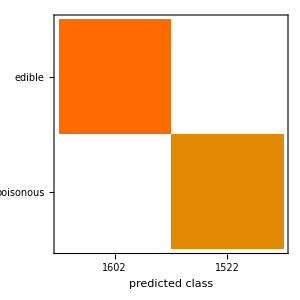

```mathematica
cm["ConfusionMatrixPlot"]
```

```mathematica
cm["ConfusionMatrix"]//Grid
```

1634 | 0 | 0
0 | 1490 | 0

```mathematica
Export["mushroom.wlnet",result]
```

mushroom.wlnet

```mathematica
CopyFile["mushroom.wlnet",CloudObject["mushroom.wlmet"]]
```

CloudObject[]

```mathematica
SetPermissions[CloudObject["mushroom.wlmet"],"Public"]
```

{All→Automatic,Owner→{Read,Write,Execute}}

```mathematica
Head[result]
```

NetGraph

```mathematica
neuralnet=result;
```

```mathematica
DumpSave["neuralnet.mx",neuralnet];
```

```mathematica
CopyFile["neuralnet.mx",CloudObject["neuralnet.mx"]]
```

CloudObject[]

```mathematica
SetPermissions[CloudObject["neuralnet.mx"],"Public"]
```

{All→Automatic,Owner→{Read,Write,Execute}}

## Building a web form for this neural network

```mathematica
formSpec=MapThread[Rule[#1,#2]&,{Rest[keys],allLabels}]
```

{cap-shape→{bell,conical,convex,flat,knobbed,sunken},cap-surface→{fibrous,grooves,scaly,smooth},cap-color→{brown,buff,cinnamon,gray,green,pink,purple,red,white,yellow},bruises→{bruises,no},odor→{almond,anise,creosote,fishy,foul,musty,none,pungent,spicy},gill-attachment→{attached,free},gill-spacing→{close,crowded},gill-size→{broad,narrow},gill-color→{black,brown,buff,chocolate,gray,green,orange,pink,purple,red,white,yellow},stalk-shape→{enlarging,tapering},stalk-root→{bulbous,club,equal,missing,rooted},stalk-surface-above-ring→{fibrous,scaly,silky,smooth},stalk-surface-below-ring→{fibrous,scaly,silky,smooth},stalk-color-above-ring→{brown,buff,cinnamon,gray,orange,pink,red,white,yellow},stalk-color-below-ring→{brown,buff,cinnamon,gray,orange,pink,red,white,yellow},veil-type→{partial},veil-color→{brown,orange,white,yellow},ring-number→{none,one,two},ring-type→{evanescent,flaring,large,none,pendant},spore-print-color→{black,brown,buff,chocolate,green,orange,purple,white,yellow},population→{abundant,clustered,numerous,scattered,several,solitary},habitat→{grasses,leaves,meadows,paths,urban,waste,woods}}

```mathematica
CloudDeploy[
FormFunction[
formSpec,
Module[{},
Get["neuralnet.mx"];
"<h1>"<>neuralnet[#]<>"</h1>"
]&,
"HTML",
AppearanceRules-><|
"Title"->"Mushroom Identifier",
"Description"->"Fill out this form to identify if your mushroom is edible or poisonous<br>(USE AT OWN RISK)"|>
],
CloudObject["mushroom-identifier"],
Permissions->"Public"
]
```

CloudObject[]

```mathematica
URLShorten[CloudObject["mushroom-identifier"]]
```

https://wolfr.am/fIPQ0oTr

```mathematica
RandomSample[validation,3]
```

{{convex,scaly,red,bruises,none,free,close,broad,brown,tapering,bulbous,smooth,smooth,gray,white,partial,white,one,pendant,brown,solitary,woods}→edible,{convex,smooth,red,no,foul,free,close,narrow,buff,tapering,missing,silky,smooth,pink,pink,partial,white,one,evanescent,white,several,paths}→poisonous,{flat,scaly,yellow,no,foul,free,close,broad,pink,enlarging,bulbous,silky,silky,buff,pink,partial,white,one,large,chocolate,several,woods}→poisonous}

```mathematica
{"flat","scaly","yellow","no","foul","free","close","broad","pink","enlarging","bulbous","silky","silky","buff","pink","partial","white","one","large","chocolate","several","woods"}
```